# Well Geometry

Robert Atkinson
21 Sept 2019

We explore the geometry of various labware.

## Administrivia

We begin by loading some handy utilities.

```mathematica
(* nothing as of yet *)
```

## Basics

```mathematica
printCell[cell_] := CellPrint[ExpressionCell[cell, "Output"]]
```

```mathematica
test[expr_] := Module[{evald},
evald = Evaluate[expr];
printCell[HoldForm[expr] -> evald];
evald]
SetAttributes[test, HoldAll]
test[7!];
% + 1
```

7!→5040

5041

```mathematica
complement[angle_] := π/2 - angle
```

```mathematica
Clear[hasImaginary]
hasImaginary[expr_] := Module[{result},
(*result = Reap[Scan[Function[ee, If[ee ≠ Conjugate[ee], Sow[True]]],{expr}, {-1, Infinity}]];*)
result = Scan[Function[ee, If[ee ≠ Conjugate[ee], Return[True]]],{expr}, {-1, Infinity}];
(*Length @ result[[2]] > 0 *)
result === True]
SetAttributes[hasImaginary, HoldAll]
test @ hasImaginary[1 + 2I];
test @ hasImaginary[30!];
```

hasImaginary[1+2 ⅈ]→True

hasImaginary[30!]→False

```mathematica
toDeg[rad_] := rad / Pi * 180
```

## Cone

### Accessing

```mathematica
assumptions[cone[h_, r_]] := h >= 0 && r >= 0
assumptions[cone[h_, α_, apexangle]]:= FullSimplify[h >= 0 && α > 0 && α < π / 2]
assumptions[cone[h_, β_, baseangle]]:= FullSimplify[assumptions[cone[h, complement[β], apexangle]]]
```

```mathematica
test @ assumptions[cone[h, α, apexangle]]
test @ assumptions[cone[h, β, baseangle]]
```

assumptions[cone[h,α,apexangle]]→h≥0&&α>0&&2 α<π

h≥0&&α>0&&2 α<π

assumptions[cone[h,β,baseangle]]→h≥0&&2 β<π&&β>0

h≥0&&2 β<π&&β>0

```mathematica
apexangle[c:cone[h_, r_]]:= Assuming[assumptions[c], ArcTan[h, r]]
apexangle[c:cone[h_, α_,apexangle]]:= α
apexangle[c:cone[h_,β_,baseangle]]:=complement[baseangle[c]]
baseangle[c:cone[h_, r_]]:= Assuming[assumptions[c], ArcTan[r, h]]
baseangle[c:cone[h_, α_,apexangle]]:= complement[α]
baseangle[c:cone[h_,β_,baseangle]]:=β
```

```mathematica
test @ apexangle[cone[h,r]];
test @ apexangle[cone[h, α,apexangle]];
test @ apexangle[cone[h, β,baseangle]];
test @ baseangle[cone[h,r]];
test @ baseangle[cone[h, α,apexangle]];
test @ baseangle[cone[h, β,baseangle]];
```

apexangle[cone[h,r]]→ArcTan[h,r]

apexangle[cone[h,α,apexangle]]→α

apexangle[cone[h,β,baseangle]]→π/2-β

baseangle[cone[h,r]]→ArcTan[r,h]

baseangle[cone[h,α,apexangle]]→π/2-α

baseangle[cone[h,β,baseangle]]→β

### Conversion

```mathematica
toCone[c:cone[h_, r_]]:= c
toCone[c:cone[h_, α_, apexangle]]:= cone[h, h Tan[α]]
toCone[c:cone[h_, β_, baseangle]] := toCone[toApexAngled[c]]

toApexAngled[c:cone[h_, r_]]:= cone[h, apexangle[c], apexangle]
toApexAngled[c:cone[h_,α_,apexangle]]:= c
toApexAngled[c:cone[h_,β_,baseangle]]:= cone[h, apexangle[c], apexangle]

toBaseAngled[c:cone[h_, r_]]:= cone[h, baseangle[c], baseangle]
toBaseAngled[c:cone[h_,α_,apexangle]]:= cone[h, baseangle[c], baseangle]
toBaseAngled[c:cone[h_,β_,baseangle]]:= c
```

```mathematica
test @ toCone[cone[h,r]];
test @ toCone[cone[h, α, apexangle]] ;
test @ toCone[cone[h, β, baseangle]];
test @ toApexAngled[cone[h,r]];
test @ toApexAngled[cone[h, α, apexangle]];
test @ toApexAngled[cone[h, β, baseangle]];
test @ toBaseAngled[cone[h,r]];
test @ toBaseAngled[cone[h, α, apexangle]];
test @ toBaseAngled[cone[h, β, baseangle]];
```

toCone[cone[h,r]]→cone[h,r]

toCone[cone[h,α,apexangle]]→cone[h,h Tan[α]]

toCone[cone[h,β,baseangle]]→cone[h,h Cot[β]]

toApexAngled[cone[h,r]]→cone[h,ArcTan[h,r],apexangle]

toApexAngled[cone[h,α,apexangle]]→cone[h,α,apexangle]

toApexAngled[cone[h,β,baseangle]]→cone[h,π/2-β,apexangle]

toBaseAngled[cone[h,r]]→cone[h,ArcTan[r,h],baseangle]

toBaseAngled[cone[h,α,apexangle]]→cone[h,π/2-α,baseangle]

toBaseAngled[cone[h,β,baseangle]]→cone[h,β,baseangle]

### Volume

```mathematica
volume[cone[h_,r_]] := Pi r r h / 3
volume[cone[h_, α_, apexangle]]:= volume[cone[h, h Tan[α]]]
volume[cone[h_, β_, baseangle]] := volume @ toApexAngled @ c
test @ volume[cone[h,r]];
test @ volume[cone[h,α,apexangle]];
test @ volume[cone[h,β,baseangle]];
```

volume[cone[h,r]]→1/3 h π r^2

volume[cone[h,α,apexangle]]→1/3 h^3 π Tan[α]^2

volume[cone[h,β,baseangle]]→volume[toApexAngled[c]]

### Height and Depth

Terminology needs fixing here.

```mathematica
depthFromVolume[c:cone[_,r_], v_] := Module[{hh}, hh /. First @ Solve[v == volume[cone[hh,r]], hh]]
test @ depthFromVolume[cone[ignored,r], volume];
```

depthFromVolume[cone[ignored,r],volume]→(3 volume)/(π r^2)

## Cylinder

### Accessing

```mathematica
assumptions[cylinder[h_, r_]] := h >= 0 && r >= 0
```

```mathematica
test @ assumptions[cylinder[h, r]];
```

assumptions[cylinder[h,r]]→h≥0&&r≥0

```mathematica
height[c:cylinder[h_, r_]]:= h
radius[c:cylinder[h_, r_]]:= r
```

### Conversion

### Volume

```mathematica
volume[cylinder[h_,r_]] := Pi r r h 
test @ volume[cylinder[h,r]];
```

volume[cylinder[h,r]]→h π r^2

### Height and Depth

```mathematica
depthFromVolume[c:cylinder[_,r_], v_] := Module[{hh}, hh /. First @ Solve[v == volume[cylinder[hh,r]], hh]]
test @ depthFromVolume[cylinder[ignored,r], volume];
```

depthFromVolume[cylinder[ignored,r],volume]→volume/(π r^2)

## Right Conical Frustum

### Accessing

```mathematica
assumptions[frustum[h_, rbottom_, rtop_]] := h≥0 && rbottom ≥ 0 && rtop ≥ 0 && rbottom > rtop
assumptions[frustum[h_, rbottom_, α_, apexangle]] := FullSimplify @ assumptions[frustum[h, rbottom, complement[α], baseangle]]
assumptions[frustum[h_, rbottom_, β_, baseangle]] := FullSimplify[h≥0 && rbottom≥ 0 && β > 0 && β < π/2]
```

```mathematica
test @ assumptions[frustum[h, rbottom, α, apexangle]];
test @ assumptions[frustum[h, rbottom, β, baseangle]];
```

assumptions[frustum[h,rbottom,α,apexangle]]→h≥0&&rbottom≥0&&2 α<π&&α>0

assumptions[frustum[h,rbottom,β,baseangle]]→h≥0&&rbottom≥0&&β>0&&2 β<π

```mathematica
apexangle[f:frustum[h_,rbottom_, α_, apexangle]]:= α
apexangle[f:frustum[h_, rbottom_, β_, baseangle]]:=complement[baseangle[f]]
apexangle[f:frustum[h_,rbottom_, rtop_]]:=Assuming[assumptions[f], ArcTan[h, rbottom-rtop]]

baseangle[f:frustum[h_, rbottom_, α_, apexangle]] := complement[ apexangle[f]]
baseangle[f:frustum[h_, rbottom_, β_, baseangle]] := β
baseangle[f: frustum[h_, rbottom_, rtop_]] := Assuming[assumptions[f], ArcTan[rbottom-rtop, h]]

baseangle[f: frustum[h_,rbottom_,rbottom_-h_ Cot[β_]]] := β

test @ apexangle[frustum[h, rbottom, rtop]];
test @ baseangle[frustum[h, rbottom, rtop]];
test @ { baseangle[frustum[1, 3, 2]], baseangle[frustum[Sqrt[3], 2, 1]]};
```

apexangle[frustum[h,rbottom,rtop]]→ArcTan[h,rbottom-rtop]

baseangle[frustum[h,rbottom,rtop]]→ArcTan[rbottom-rtop,h]

{baseangle[frustum[1,3,2]],baseangle[frustum[√3,2,1]]}→{π/4,π/3}

```mathematica
height[f:frustum[h_, rbottom_, α_, apexangle]] := h
height[f:frustum[h_, rbottom_, β_, baseangle]] := h
height[f:frustum[h_, rbottom_, rtop_]] := h
```

```mathematica
rbottom[f:frustum[h_, rbottom_, α_, apexangle]] := rbottom
rbottom[f:frustum[h_, rbottom_, β_, baseangle]] := rbottom
rbottom[f:frustum[h_, rbottom_, rtop_]] := rbottom
```

```mathematica
Tan[α] / Cot[complement[α]] == 1
rtop[f:frustum[h_, rbottom_, α_, apexangle]] := Assuming[assumptions[f], rbottom - h Tan[α]]
rtop[f:frustum[h_, rbottom_, β_, baseangle]] := Assuming[assumptions[f], rbottom - h Cot[β]]
rtop[f:frustum[h_, rbottom_, rtop_]] := rtop
rtop[f:frustum[h_,rbottom_,ArcTan[rbottom_-rtop_,h_],baseangle]] := rtop
test @ rtop[frustum[h,rbottom,α, apexangle]];
test @ rtop[frustum[h,rbottom,β, baseangle]];
test @ rtop[frustum[h,rbottom,rtop]];
```

True

rtop[frustum[h,rbottom,α,apexangle]]→rbottom-h Tan[α]

rtop[frustum[h,rbottom,β,baseangle]]→rbottom-h Cot[β]

rtop[frustum[h,rbottom,rtop]]→rtop

### Conversion

```mathematica
toFrustum[f: frustum[h_, rbottom_, α_, apexangle]]:= frustum[h,rbottom,rtop[f]]
toFrustum[f: frustum[h_, rbottom_, β_, baseangle]] := frustum[h,rbottom,rtop[f]]
toFrustum[f: frustum[h_, rbottom_, rtop_]] := f

toApexAngled[f:frustum[h_, rbottom_, α_, apexangle]] := f
toApexAngled[f:frustum[h_, rbottom_, β_, baseangle]] := frustum[h, rbottom, complement[β], apexangle]
toApexAngled[f:frustum[h_, rbottom_, rtop_]] := frustum[h, rbottom, apexangle[f], apexangle]

toBaseAngled[f:frustum[h_, rbottom_, α_, apexangle]] :=frustum[h, rbottom, complement[α], baseangle]
toBaseAngled[f:frustum[h_, rbottom_, β_, baseangle]] := f
toBaseAngled[f:frustum[h_, rbottom_, rtop_]] := frustum[h, rbottom, baseangle[f], baseangle]
```

```mathematica
test @ toFrustum @ frustum[h, rbottom, β, baseangle];
test @ toBaseAngled @ %;
test @ toApexAngled @ %%;
test @ toFrustum @  %;
test @ toBaseAngled @  %%;
```

toFrustum[frustum[h,rbottom,β,baseangle]]→frustum[h,rbottom,rbottom-h Cot[β]]

toBaseAngled[%]→frustum[h,rbottom,β,baseangle]

toApexAngled[%%]→frustum[h,rbottom,π/2-β,apexangle]

toFrustum[%]→frustum[h,rbottom,rbottom-h Cot[β]]

toBaseAngled[%%]→frustum[h,rbottom,β,baseangle]

```mathematica
test @ toBaseAngled @ frustum[h, rbottom, rtop];
test @ toFrustum @ %;
```

toBaseAngled[frustum[h,rbottom,rtop]]→frustum[h,rbottom,ArcTan[rbottom-rtop,h],baseangle]

toFrustum[%]→frustum[h,rbottom,rtop]

### Volume

```mathematica
coneHeight[f:frustum[h_, rbottom_, α_, apexangle]]:=rbottom / Tan[α]
coneHeight[f:frustum[h_, rbottom_, β_, baseangle]]:=rbottom / Cot[β] 
coneHeight[f:frustum[h_, rbottom_, rtop_]] := coneHeight @ toApexAngled @ f

test @ coneHeight[frustum[h,rbottom,α,apexangle]];
test @ coneHeight[frustum[h,rbottom,β,baseangle]];
test @ toApexAngled @ frustum[h,rbottom,β,baseangle];
test @ coneHeight@ %;
test @ coneHeight[frustum[h,rbottom,rtop]];
test @ coneHeight[frustum[1, 3, 2]];
```

coneHeight[frustum[h,rbottom,α,apexangle]]→rbottom Cot[α]

coneHeight[frustum[h,rbottom,β,baseangle]]→rbottom Tan[β]

toApexAngled[frustum[h,rbottom,β,baseangle]]→frustum[h,rbottom,π/2-β,apexangle]

coneHeight[%]→rbottom Tan[β]

coneHeight[frustum[h,rbottom,rtop]]→(h rbottom)/(rbottom-rtop)

coneHeight[frustum[1,3,2]]→3

```mathematica
volume[f: frustum[h_, rbottom_, rtop_]] := volume[cone[coneHeight[f], rbottom]] - volume[cone[coneHeight[f]-h, rtop]] // FullSimplify
volume[f: frustum[h_, rbottom_, α_, apexangle]]:= volume[cone[coneHeight[f],α,apexangle]]-volume[cone[coneHeight[f]-h, α,apexangle]] // FullSimplify
volume[f: frustum[h_, rbottom_, β_, baseangle]]:= volume @ toApexAngled[f]

v=test @ volume[frustum[h,r1,r2]]; (* compare to textbook answer 1/3 h π (r1^2+r1 r2+r2^2) *)
vα=test @ volume[frustum[h,r,α,apexangle]];
test @ toFrustum @ frustum[h,r,α,apexangle];
vα2 = test @ volume[%];
vβ=test @ volume[frustum[h, r, β,baseangle]];
test @ (v /. r2 -> 0);
Clear[v, vα, vα2, vβ]
```

volume[frustum[h,r1,r2]]→1/3 h π (r1^2+r1 r2+r2^2)

volume[frustum[h,r,α,apexangle]]→1/3 h π (3 r^2+h Tan[α] (-3 r+h Tan[α]))

toFrustum[frustum[h,r,α,apexangle]]→frustum[h,r,r-h Tan[α]]

volume[%]→1/3 h π (3 r^2+h Tan[α] (-3 r+h Tan[α]))

volume[frustum[h,r,β,baseangle]]→1/3 h π (3 r^2+h Cot[β] (-3 r+h Cot[β]))

(v/.r2→0)→1/3 h π r1^2

### Height and Depth

#### Experimenting

In the below,  the ‘Solve’ calls generate three solutions each. Which index to choose is unfortunately data-dependent.

```mathematica
heightFromVolumeExperiment[f:frustum[h_, rbottom_, rtop_], vol_, index_] := Module[{hh, ff, eqn, solns},
(* we're looking for a frustum with same base angle and bottom radius, but different height *)
ff = frustum[hh,rbottom, baseangle[f], baseangle];
eqn = FullSimplify[vol == volume[ff], assumptions[f] && vol ≥ 0];
solns = Solve[eqn, hh];
FullSimplify[hh /. solns[[index]], assumptions[f] && vol ≥ 0]
]
heightFromVolumeExperiment[f:frustum[h_, rbottom_, rtop_], vol_] := heightFromVolumeExperiment[f, vol, 2]
generalFrustum = frustum[h, r1, r2]
test @ heightFromVolumeExperiment[generalFrustum, vol];
```

frustum[h,r1,r2]

heightFromVolumeExperiment[generalFrustum,vol]→(2 h π^(1/3) r1+ⅈ (ⅈ+√3) h^(2/3) (-h π r1^3+3 (r1-r2) vol)^(1/3))/(2 π^(1/3) (r1-r2))

```mathematica
heightFromVolumeExperiment[f:frustum[ignored_, rbottom_, α_, apexangle], vol_, index_] := Module[{hh, ff, eqn, solns},
(* we're looking for a frustum with same base angle and bottom radius, but different height *)
ff = frustum[hh,rbottom, baseangle[f], baseangle];
eqn = FullSimplify[vol == volume[ff], assumptions[f] && vol ≥ 0];
solns = Solve[eqn, hh];
FullSimplify[hh /. solns[[index]], assumptions[f] && vol ≥ 0]
]
heightFromVolumeExperiment[f:frustum[ignored_, rbottom_, α_, apexangle], vol_] := heightFromVolumeExperiment[f, vol, 1]
generalApexFrustum = frustum[h, r, α, apexangle]
test @ heightFromVolumeExperiment[generalApexFrustum, vol];
```

frustum[h,r,α,apexangle]

heightFromVolumeExperiment[generalApexFrustum,vol]→Cot[α] (r-(r^3-(3 vol Tan[α])/π)^(1/3))

```mathematica
heightFromVolumeExperiment[f:frustum[ignored_, rbottom_, β_, baseangle], vol_, index_] := Module[{hh, ff, eqn, solns},
(* we're looking for a frustum with same base angle and bottom radius, but different height *)
ff = frustum[hh,rbottom, baseangle[f], baseangle];
eqn = FullSimplify[vol == volume[ff], assumptions[f] && vol ≥ 0];
solns = Solve[eqn, hh];
FullSimplify[hh /. solns[[index]], assumptions[f] && vol ≥ 0]
]
heightFromVolumeExperiment[f:frustum[ignored_, rbottom_, β_, baseangle], vol_] := heightFromVolumeExperiment[f, vol, 2]
generalBaseFrustum = frustum[h, r, β, baseangle]
test @ heightFromVolumeExperiment[generalBaseFrustum, vol];
```

frustum[h,r,β,baseangle]

heightFromVolumeExperiment[generalBaseFrustum,vol]→r Tan[β]+1/2 (1-ⅈ √3) (r^3-(3 vol Cot[β])/π)^(1/3) Tan[β]

#### Final

```mathematica
heightFromVolume[f:frustum[ignored_, rbottom_, α_, apexangle], vol_] := Module[{hh, ff, eqn, solns},
(* we're looking for a frustum with same base angle and bottom radius, but different height *)
ff = frustum[hh,rbottom, baseangle[f], baseangle];
eqn = FullSimplify[vol == volume[ff], assumptions[f] && vol ≥ 0];
solns = Solve[eqn, hh];
FullSimplify[hh /. solns[[1]], assumptions[f] && vol ≥ 0]
]
generalApexFrustum = frustum[h, r, α, apexangle]
test @ heightFromVolume[generalApexFrustum, vol];
```

frustum[h,r,α,apexangle]

heightFromVolume[generalApexFrustum,vol]→Cot[α] (r-(r^3-(3 vol Tan[α])/π)^(1/3))

```mathematica
heightFromVolume[f:frustum[ignored_, rbottom_, rtop_], vol_] := Module[{general, h, r1, r2, α},
general = frustum[h, r1, α, apexangle];
heightFromVolume[, vol] // FullSimplify]
generalFrustum = frustum[h, r1, r2]
test @ toApexAngled @ generalFrustum
test @ heightFromVolume[generalFrustum, vol];
test @ (heightFromVolume[generalApexFrustum, vol] /. { α -> apexangle[generalFrustum]}); (* works !*)
FullSimplify @ %
```

frustum[h,r1,r2]

toApexAngled[generalFrustum]→frustum[h,r1,ArcTan[h,r1-r2],apexangle]

frustum[h,r1,ArcTan[h,r1-r2],apexangle]

heightFromVolume[generalFrustum,vol]→(h r1 (r1-r2)+((-h^2 (r1-r2)^3 (h π r1^3-3 r1 vol+3 r2 vol))^(1/3))/π^(1/3))/(r1-r2)^2

(heightFromVolume[generalApexFrustum,vol]/.{α→apexangle[generalFrustum]})→(h (r-(r^3-(3 (r1-r2) vol)/(h π))^(1/3)))/(r1-r2)

(h (r-(r^3+(3 (-r1+r2) vol)/(h π))^(1/3)))/(r1-r2)

```mathematica
heightFromVolume[f:frustum[ignored_, rbottom_, β_, baseangle], vol_] := heightFromVolume[toApexAngled[f], vol] // FullSimplify
generalBaseFrustum = frustum[h, r, β, baseangle]
test @ heightFromVolume[generalBaseFrustum, vol];
```

frustum[h,r,β,baseangle]

heightFromVolume[generalBaseFrustum,vol]→(r-(r^3-(3 vol Cot[β])/π)^(1/3)) Tan[β]

#### Testing

frustum[1,2,π/9,apexangle]

{1/3 π (12+(-6+Tan[π/9]) Tan[π/9]),10.4182,frustum[1.,2.,1.63603]}

2 Cot[π/9]-Cot[π/9]^(2/3) (-(3 v)/π+8 Cot[π/9])^(1/3)

8.88178×10^-16
0.0079693
0.0159618
0.0239777
0.0320172
0.0400804
0.0481675
0.0562787
0.0644141
0.072574
0.0807586

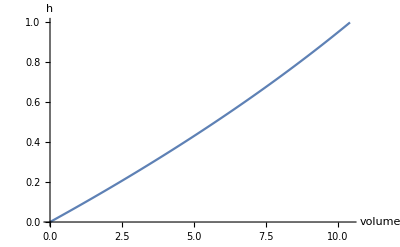

-Graphics-

```mathematica
example = frustum[1, 2, π/9, apexangle]
{ volume[example], volume[example] // N , N @ toFrustum @ example}
expr = heightFromVolume[example,v]
expr /. v -> # & /@ Range[0, 1, .1] // ColumnForm
Plot[expr, {v, 0, volume[example]}, AxesLabel->{"volume", "h"}]
Plot[heightFromVolume[example,v], {v, 0, volume[example]}, AxesLabel->{"volume", "h"}]
```

```mathematica
example = frustum[Sqrt[3], 2, 1];
{ volume[example], volume[example] // N , 180 / Pi * (apexangle @ toApexAngled @ example) }
expr = test @ heightFromVolume[example,v];
test@ heightFromVolume[example,0];
test @  (heightFromVolume[generalFrustum, vol] /. {h -> Sqrt[3], r1 -> 2, r2 -> 1});
test @  N @(expr /. v -> 0);
(*heightFromVolume[frustum[h, r1, r2], v] /. {h -> Sqrt[3], r1-> 2, r2-> 1} // FullSimplify
expr/. v -> # & /@ Range[0, 1, .1] // ColumnForm
Plot[expr, {v, 0, volume[example]}, AxesLabel->{"volume", "h"}]
Plot[ heightFromVolume[example,v], {v, 0, volume[example]}, AxesLabel->{"volume", "h"}]*)
```

{(7 π)/(√3),12.6966,30}

heightFromVolume[example,v]→2 √3+(-24 √3+(9 v)/π)^(1/3)

heightFromVolume[example,0]→0

(heightFromVolume[generalFrustum,vol]/.{h→√3,r1→2,r2→1})→2 √3+(3/π)^(1/3) (-8 √3 π+3 vol)^(1/3)

N[expr/.v→0]→5.19615+3. ⅈ

```mathematica
example = frustum[1, 2, π/6, baseangle]
{ volume[example], volume[example] // N }
expr = heightFromVolume[example,v]
expr /. v -> # & /@ Range[0, 1, .1] // ColumnForm
Plot[expr ,{v, 0, volume[example]}, AxesLabel->{"volume", "h"}]
Plot[heightFromVolume[example,v], {v, 0, volume[example]}, AxesLabel->{"volume", "h"}]
```